```mathematica
f1[t_,x_,y_]:=t^2-y*Sin[x];
f2[t_,x_,y_]:= Cos[t]*x+y^2-t;
```

0.1

0.2

0.05

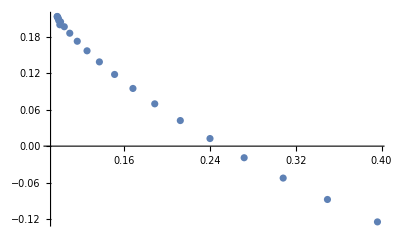

```mathematica
x[0]=0.1
y[0]=0.2
h=0.05
Do[{x[n]=x[n-1]+h*f1[(n-1)*h,x[n-1],y[n-1]],
   y[n]=y[n-1]+h*f2[(n-1)*h,x[n-1],y[n-1]]},{n,1,20}]
a=ListPlot[Table[{x[n],y[n]},{n,0,20}]]
```

```mathematica
N[x[20]]
N[y[20]]
```

0.396206

-0.12485

```mathematica
Clear[x];
Clear[y];
```

```mathematica
s=NDSolve[{x'[t]==t^2-y[t]*Sin[x[t]], y'[t]==Cos[t]*x[t]+y[t]^2-t,{x[0]==.1,y[0]==.2}},{x,y},{t,1}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

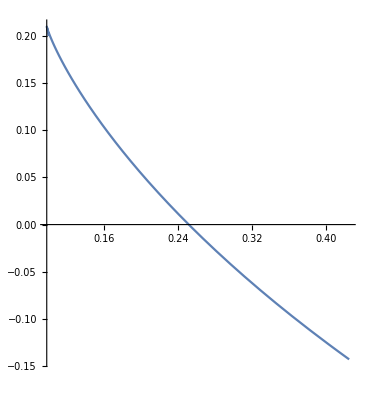

```mathematica
b=ParametricPlot[Evaluate[{x[t],y[t]}/.s], {t,0,1}]
```

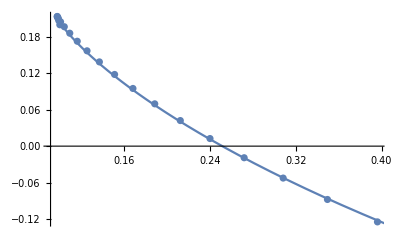

```mathematica
Show[a,b]
```

```mathematica
x[1]/.s
y[1]/.s
```

{0.424631}

{-0.142956}

```mathematica
Clear[x];
Clear[y];
```

```mathematica
x[0]=0.1
y[0]=0.2
```

0.1

0.2

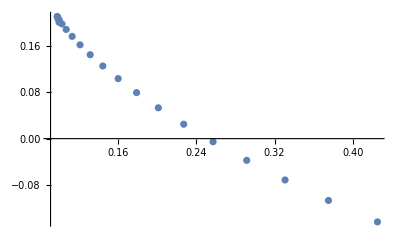

```mathematica
Do[{k11=h f1[h n,x[n],y[n]];
k12=h f2[h n,x[n],y[n]];
k21=h f1[h (n+1),x[n]+k11,y[n]+k12];
k22=h f2[h (n+1),x[n]+k11,y[n]+k12];
x[n+1]=x[n]+ .5(k11+k21),
y[n+1]=y[n]+.5(k12+k22)},{n,0,20}]

c=ListPlot[Table[{x[n],y[n]},{n,0,20}]]
```

```mathematica
N[x[20]]
N[y[20]]
```

0.425064

-0.143082

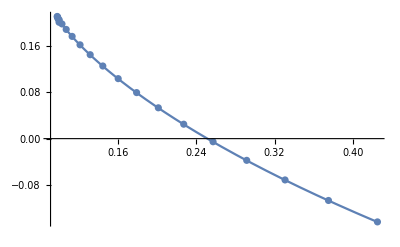

```mathematica
Show[c,b]
```

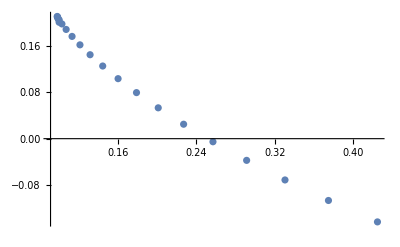

```mathematica
Clear[x];
Clear[y];
x[0]=0.1;
y[0]=0.2;


Do[{k11= f1[h n,x[n],y[n]];
k12= f2[h n,x[n],y[n]];
k21 = f1[h (n+0.5),x[n]+k11(h/2),y[n]+k12(h/2)];
k22 = f2[h (n+0.5),x[n]+k11(h/2),y[n]+k12(h/2)];
k31 = f1[h(n+0.5), x[n]+k21(h/2), y[n]+k22(h/2)];
k32 = f2[h(n+0.5), x[n]+k21(h/2), y[n]+k22(h/2)];
k41 = f1[h(n+1), x[n]+k31*h, y[n]+k32*h];
k42 = f2[h(n+1), x[n]+k31*h, y[n]+k32*h];
x[n+1]=x[n]+ (h/6)(k11+2*k21+2*k31+k41),
y[n+1]=y[n]+(h/6)(k12+2*k22+2*k32+k42)},{n,0,20}]

d=ListPlot[Table[{x[n],y[n]},{n,0,20}]]
```

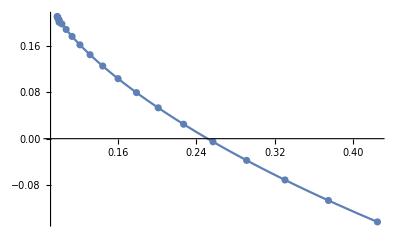

```mathematica
Show[d,b]
```

```mathematica
N[x[20]]
N[y[20]]
```

0.424631

-0.142956

```mathematica
Clear[x];
Clear[y];

sol = NDSolve[{x'''[t]+Sin[t]*x''[t]+x[t]^2*x'[t]==1, x''[0]==1, x'[0]==0, x[0]==1}, x,{t,1}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
x[1]/.sol
```

{1.56183}

```mathematica
Clear[x];
Clear[y];
Clear[z];
Clear[h];
Clear[f1];
Clear[f2];
Clear[f3];
```

```mathematica
f1[y_]:=y;
f2[z_]:=z;
f3[t_,x_,y_,z_]:=1-(Sin[t]*z)-(x^2 y);
```

```mathematica
x[0]=1;
y[0]=0;
z[0]=1;
h = 0.01;
```

```mathematica
Do[{k11=f1[y[n]];
k12=f2[z[n]];
k13=f3[h*n, x[n], y[n], z[n]];
k21=f1[y[n]+(h*k12)];
k22=f2[z[n]+(h*k13)];
k23= f3[h*(n+1), x[n]+(k11*h), y[n]+(k12*h), z[n]+k13*h];
x[n+1]=x[n]+ ((h/2)*(k11+k21)),
y[n+1]=y[n]+((h/2)*(k12+k22)),
z[n+1]= z[n]+((h/2)*(k13+k23))},{n,0,100}]
```

```mathematica
N[x[100]]
```

1.56185

```mathematica
1.5618524268220324

Clear[x,y,f1,f2,f3,h];
```

1.56185

```mathematica
h = 0.05;
y1[0]=9;
y2[0]=-1;

f1[y2_]:=y2;
f2[y1_, y2_]:= 2 + ((4*y1)/3) + ((2*y2)/3);
```

20 t

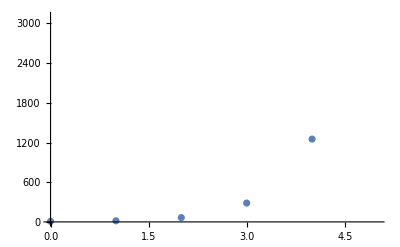

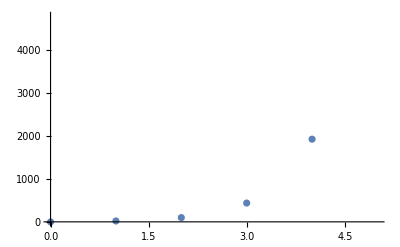

```mathematica
Do[{y1[n+1]=y1[n]+h*f1[y2[n]],
   y2[n+1]=y2[n]+h*f2[y1[n],y2[n]]},{n,0,100}]
f4[t_] = t*20
q=ListPlot[Table[{t,y1[f4[t]]},{t,0,5}]]
r = ListPlot[Table[{t,y2[f4[t]]},{t,0,5}]]
```

```mathematica
N[y1[100]]
```

5500.37

```mathematica
Clear[y1,y2]
```

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

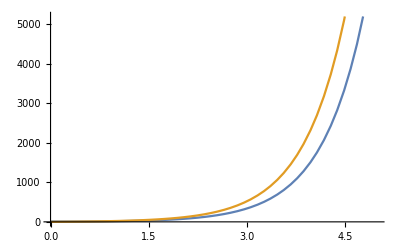

```mathematica
solution = NDSolve[{y1'[t]==y2[t], y2'[t]==2+((4*y1[t])/3)+((2*y2[t])/3),{y1[0]==9,y2[0]==-1}},{y1,y2},{t,5}]
Nplot = Plot[Evaluate[{y1[t],y2[t]}/.solution], {t,0,5}]
```

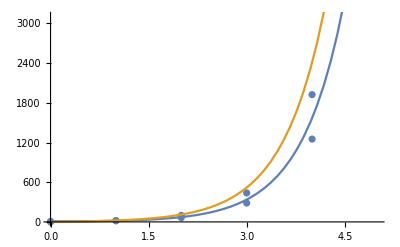

```mathematica
Show[q,r, Nplot]
```

```mathematica
y1[5]/.solution
```

{7280.65}

```mathematica
Clear[x,t,y]
```

```mathematica
r = NDSolve[{x'[t] == -(x[t]^2) + 13 + Sqrt[x[t]], x[0]==3}, x, {t,0,5}]
```

{{x→InterpolatingFunction[…]}}

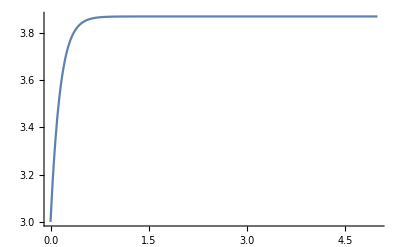

```mathematica
Plot[Evaluate[x[t]/.r], {t,0,5}, PlotRange->All]
```